```mathematica
(* Que: Maximize x+y
s.t. x+y≤1
	 -3x+y≥3
	 x≥0 && y≥0
*)

Maximize[{ x+y,x+y≤1 && -3 x+y ≥3 && x≥0 && y≤0 },{x,y}]
```

Maximize::infeas: There are no values of {x,y} for which the constraints x+y≤1&&-3 x+y≥3&&x≥0&&y≤0 are satisfied and the objective function x+y is real valued.

{-∞,{x→Indeterminate,y→Indeterminate}}

```mathematica
RegionPlot[{ x+y≤1 && -3x+y≥3 && x≥0 && y≥0 },{x,-5,5},{y,-5,5},Frame->False,Axes->True]
```

-Graphics-

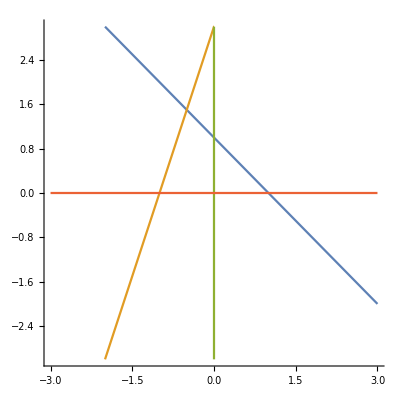

```mathematica
ContourPlot[{ x+y==1,-3 x+y==3,x==0,y==0 },{x,-3,3},{y,-3,3},Frame->False,Axes->True]
```